## 作用量

我们在经典力学中就开始接触作用量了，从经典力学里面的三种表述方法，到量子力学的三种表述方法，作用量现身的频率可谓不低。

那么什么是作用量？

### 经典力学

经典力学有三种表述方法，分别是 Euler-Lagrange 方程，Hamiltonian 正则方程以及 Hamiltonian-Jacobi 理论。这三种理论中，Euler-Lagrange 方程和 Hamiltonian-Jacobi 理论都需要用到作用量。那么作用量在经典力学中，是什么意思呢？

#### Action Principal

作用量原理是拉氏形式中最核心的内容。在这里，作用量是拉氏量在时间上的积分，

S=(∫_ti)^tf L(q(t),q'(t),t)dt=S(q(t))

也就是说，拉氏量是时间t，广义坐标q(t)，广义坐标对时间的导数q’(t) 的函数。但是作用量却只是广义坐标q(t)的函数。

我们先不管作用量原理，先看看这个作用量到底是什么意思。在一个保守力系中，拉氏量可以写成动能减去势能

L=T-V

那么作用量就是

S=(∫_ti)^tf(T-V)dt

这个很有趣。当我们选定一条路径之后，例如我们选定一个经典路径之后，作用量就是动能和势能对时间的曲线之间的面积。这样说起来太抽象，我们可以看一个自由落体运动的例子（从 x=0 开始沿 x 轴负方向下落）：

L=1/2 m x'^2-m g x

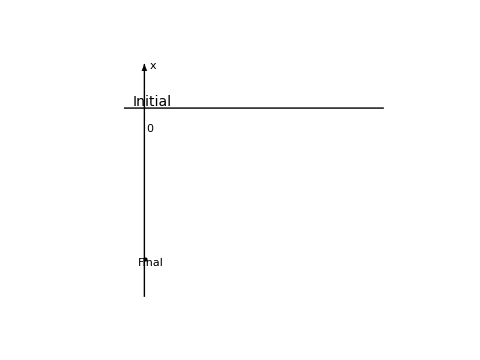

为了方便假定质量 m 为 1，那么如果我们选定经典轨道，那么就可以把动能和势能随着时间的变化关系画出来。

（经典轨道中，动能 T=(m g^2 t^2 )/2，势能 V=  - (m g^2 t^2) /2 ）

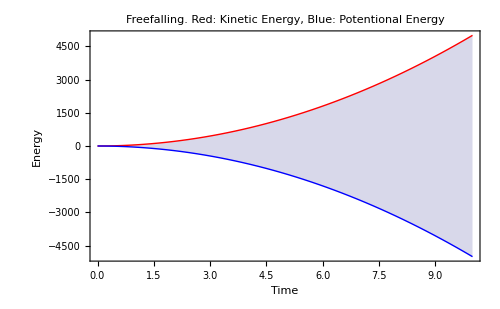

```mathematica
Plot[{100 t^2/2,-100 t^2/2},{t,0,10},PlotLabel->"Freefalling. Red: Kinetic Energy, Blue: Potentional Energy",PlotStyle->{Red,Blue},FrameLabel->{"Time","Energy"},Filling->{1->{2}},Frame->True,ImageSize->500]
```

所以，对于这条经典路径，上面的阴影部分面积就是我们的路径积分的结果，即动能和势能的能量差值在整个时间上面的积分。

那么如果我们不是选取的经典路径呢？比如我们选取了这样一条路径：